## Initialization code

### Create example data sets

```mathematica
closeCellGroup[] := (SelectionMove[EvaluationCell[], Next,Cell]; 
FrontEndExecute[FrontEndToken["SelectionCloseUnselectedCells"]])
```

```mathematica
simuationSize=168357;
```

In this section, I generate the data I need to verify that the code changes I am making work correctly with your data.  The data I generate has two major short comings.  First, the multivariate distributions I estimate for your coordinate and velocity data are far from your data.  Especially, for example, the mean of the z-coordinate is totally incorrect and although the mean vector for the x and y coordinate appear “acceptable” for these examples, the variance is smaller.  You will see this in the ListPlots of this data.  Also, the Tag data sample I had to work with was all -1 values. So when I generated a vector of similar percentage occurrence of LMC/DM tags, the sequence of -1 and 1’s was random and fully independent of the coordinate and velocity data.  This means the “cuts” based on tag type are totally off-the-wall.  Nonetheless, the simulated values maintain an appropriate sample size and permit me to roughly verify that my code is okay.

In the “Notebook data” section below I reuse the displayed values in your original notebook

In the “Estimated sample data distribution parameters” section I use the Mathematica EstimatedDistribution to estimate the distribution characteristics of your variables in order to simulate similar sized datasets.  There are only 6 values each for the coordinate and velocity sample distributions so the parameter estimates are useless for anything but testing the code snippets.  I assume that the generating processes for both the coordinates and the velocities are approximated by a Multivariate Normal Distribution.  Then I use the estimated mean vectors and covariance matrices to simulate 168,357 data points.

In the “Multivariate Normal mean and covariance from simulated data” section, I use the RandomVariate command to generate the simulated data  Then I use “FindDistributionParameters” to find estimate the distribution parameters of the simulate data.  You can compare this to the “actual” distribution parameters of your data.

I repeat this process for the velocity data.

There are 76 values for the LMC tag data.  From this data, I generate a vector of {-1’s and 1’s} weighted to produce the same percentage of LMC particles in the same sized vector as in your sample.  This is, of course, independent from and not correlated with the coordinate and velocity data.  This allows the code to be simulated but not the results.

#### DM coordinate variables

Notebook data

```mathematica
MatrixForm[dmCords00Sample={{0.016431426629424095,-0.1076788678765297,0.03446260467171669},{-0.08331732451915741,-0.005956035573035479,0.18741817772388458},{0.23650655150413513,0.05569346994161606,0.0347386933863163},{-4.803868293762207,0.7528245449066162,-11.71234130859375},{-1.302531123161316,-8.16396427154541,-4.614678382873535},{-1.0871785879135132,-0.7993932962417603,-4.996247291564941}}];
```

Estimated sample data distribution parameters

```mathematica
edistCoords=EstimatedDistribution[dmCords00Sample, MultinormalDistribution[Array[μ,3],Array[s,{3,3}]]]
```

MultinormalDistribution[{-1.17066,-1.37808,-3.51111},{{2.96603,-0.296873,7.17307},{-0.296873,9.4127,0.63605},{7.17307,0.63605,18.2512}}]

Multivariate Normal mean and covariance from simulated data

```mathematica
dmCords00RV=RandomVariate[edistCoords,simuationSize];
fdistpar=FindDistributionParameters[dmCords00RV, MultinormalDistribution[Array[μ,3],Array[s,{3,3}]]]
```

{μ[1]→-1.17398,μ[2]→-1.38326,μ[3]→-3.51943,s[1,1]→2.98369,s[1,2]→-0.301257,s[1,3]→7.21484,s[2,1]→-0.301257,s[2,2]→9.46185,s[2,3]→0.637064,s[3,1]→7.21484,s[3,2]→0.637064,s[3,3]→18.3508}

#### DM velocity variables

Notebook data

```mathematica
MatrixForm[dmVels00Sample={{36.43170166015625,-9.138969421386719,-26.757831573486328},{-24.890954971313477,-21.605627059936523,-3.0834414958953857},{-9.940251350402832,-14.906100273132324,33.107540130615234},{-169.15914916992188,139.89755249023438,-290.9612121582031},{-104.96575164794922,120.04015350341797,-352.1723937988281},{-103.65585327148438,-1.9502073526382446,-415.2244873046875}}]
Dimensions@%
```

(36.4317 | -9.13897 | -26.7578
-24.891 | -21.6056 | -3.08344
-9.94025 | -14.9061 | 33.1075
-169.159 | 139.898 | -290.961
-104.966 | 120.04 | -352.172
-103.656 | -1.95021 | -415.224)

{6,3}

Estimated sample data distribution parameters

```mathematica
edist=EstimatedDistribution[dmVels00Sample, MultinormalDistribution[Array[μ,3],Array[s,{3,3}]]]
```

MultinormalDistribution[{-62.6967,35.3895,-175.849},{{4806.26,-3732.85,10307.9},{-3732.85,4540.47,-7502.17},{10307.9,-7502.17,32896.7}}]

Multivariate Normal mean and covariance from simulated data

```mathematica
dmVels00RV=RandomVariate[edist,simuationSize];
fdistpar=FindDistributionParameters[dmVels00RV, MultinormalDistribution[Array[μ,3],Array[s,{3,3}]]]
```

{μ[1]→-62.7166,μ[2]→35.5733,μ[3]→-175.585,s[1,1]→4771.06,s[1,2]→-3705.42,s[1,3]→10241.8,s[2,1]→-3705.42,s[2,2]→4520.83,s[2,3]→-7428.94,s[3,1]→10241.8,s[3,2]→-7428.94,s[3,3]→32830.2}

#### LMC_tag for each DM particle variable

```mathematica
Notebook data
```

```mathematica
dmTag00Sample={-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.};
Length@dmTag00Sample
```

76

Simulated LMC tag data

```mathematica
dmTag00RV=RandomChoice[{.17,1-.17}->{-1,1},simuationSize];
Length@dmTag00RV
```

168357

```mathematica
generatedData={dmCords00RV,dmVels00RV,dmTag00RV};
```

## Prolog - Simulate a dataset from your sample

The code for this section is at the top of the notebook.  Only the resulting list of variable matrices and vectors is at the bottom of this section.  The code to create these simulated variables and resulting data set is set to initialize when your run the assignments below (generatedData and dmData).  A popup will inform you of this.

Notation

I have mostly kept all your variable names; but I have appended “RV” to the name so that you can easily equate the variables when they are created and used.

General observation

You are using an “procedural” style of programming (e.g., For and Do loops, the Table command is a Do loop).  This is fine and not “wrong” (as there is no “right” way).  However, Mathematica performs better (faster) and is more concise when one uses a functional or rule-based style.  So, most of my notes below change your For loops to a hybrid function/pattern matching style.

I use Join to combine your tags,  coordinates and velocities into one dataset (as you are assuming the sequence of data in each individual data set is rebated, i.e., tag “i” is for coordinates “i” and velocity “i”).  There are several ways to do this.  The Join command requires that the dmTag00 vector be a matrix, so I create a single column matrix with the Partition command.  Then use the Select command to select the data rows based on the tag value (which in this case is in column 7 of the data matrix)

```mathematica
generatedData={dmCords00RV,dmVels00RV,dmTag00RV};
dmData=Join[dmCords00RV,dmVels00RV,Partition[dmTag00RV,1],2];
```

## Notes on alternate code formulations

### CHECKING NUMBER OF LMC PARTICLES

Use Count in place of your For loop.  Count counts the elements of a list by pattern matching.  It counts any value, symbolized by the  pattern “x_ “ that meets the Condition (“/;” ) of x == - 1.  You can use the operator form if it makes more sense to you, i.e., “Count x’s, where x ≤ 1 in the ‘dmTag00’ list (or array or association, etc.)”.  First, I create a random sample of tags (either -1 or 1) weighted by the percentage in your work.

```mathematica
numLMCRV=Count[dmTag00RV,x_/;x<=-1]
Count[x_/;x==-1][dmTag00RV]   (* Operator form *)
N[numLMCRV/simuationSize,2]
```

28349

28349

0.17

### SELECTING THE X-Y COORDINATES FOR DATA DISPLAY

```mathematica
dmCords00xyRV=dmCords00RV⟦All,;;2⟧;
```

Use the Part command with ALL instead of the Table command (which is a Do loop) to select the columns of your coordinates matrix.  When the columns are beside one another you can use the convenient shorthand with “;;” (e.g., x and y).  When the columns are separated by intervening columns, use a List  to indicate which columns are to be selected (eg.g, x & z).

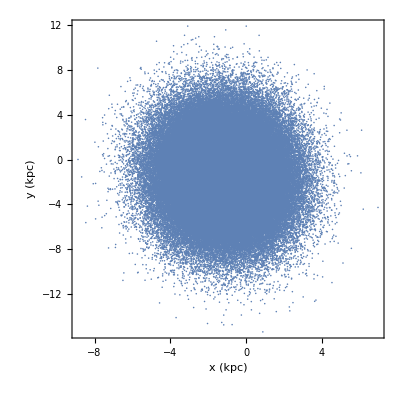

```mathematica
ListPlot[dmCords00xyRV, FrameLabel->{"x (kpc)","y (kpc)"}, Axes->True, Frame->True, FrameStyle->Directive[Thickness[0.003],FontSize->15,FontFamily->"Times"],FrameTicksStyle->Directive[Black, 15], LabelStyle->Directive[14], AspectRatio->1]
closeCellGroup[]
```

```mathematica
dmCords00xzRV=dmCords00RV⟦All,{1,3}⟧;
```

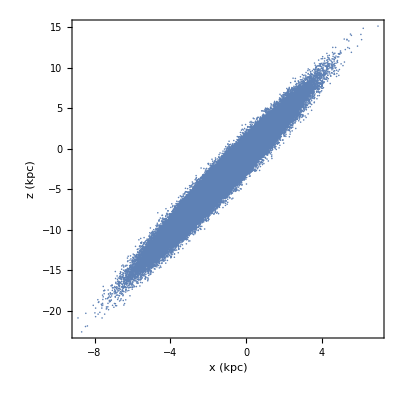

```mathematica
ListPlot[dmCords00xzRV, FrameLabel->{"x (kpc)","z (kpc)"}, Axes->True, Frame->True, FrameStyle->Directive[Thickness[0.003],FontSize->15,FontFamily->"Times"],FrameTicksStyle->Directive[Black, 15], LabelStyle->Directive[14], AspectRatio->1]
closeCellGroup[]
```

### MW-Only and LMC-Only Cuts

```mathematica
Dimensions@dmData
dmData⟦;;10⟧//MatrixForm
```

{168357,7}

(-2.47785 | -1.00983 | -7.15982 | -145.361 | 124.023 | -91.606 | 1
1.52193 | -0.589729 | 3.87241 | -42.2461 | -23.1733 | -84.6908 | 1
-0.216805 | -0.592979 | -2.01632 | -118.525 | 152.73 | -212.518 | 1
-3.66249 | 2.47318 | -9.79143 | -202.932 | 159.896 | -468.74 | 1
-1.28155 | -2.20258 | -3.78885 | -125.168 | 71.2415 | -411.812 | -1
-0.402581 | -2.4904 | -2.75741 | -11.4254 | 23.564 | -52.1388 | 1
-0.671576 | 4.82283 | -0.827486 | 76.2259 | -75.0738 | 152.624 | 1
-0.239572 | -6.57774 | -2.50662 | -27.9264 | 12.2635 | 6.28465 | 1
0.0393951 | 0.816605 | -1.33353 | -13.1625 | 18.8047 | -125.949 | 1
-2.06069 | 3.98463 | -4.78312 | -205.659 | 110.419 | -448.857 | 1)

```mathematica
lmcData=Select[dmData,#⟦7⟧==-1&];
Dimensions@lmcData
lmcData⟦;;10⟧//MatrixForm
```

{28349,7}

(-1.28155 | -2.20258 | -3.78885 | -125.168 | 71.2415 | -411.812 | -1
-2.81823 | 0.0348481 | -8.90025 | -119.602 | 126.61 | -170.51 | -1
-2.18787 | 1.3707 | -4.12511 | -41.2369 | 34.8234 | 43.575 | -1
0.43191 | -6.90119 | 0.806883 | -91.9157 | 27.7269 | -310.718 | -1
-1.16992 | 0.636815 | -2.75944 | -12.3822 | 33.4337 | -127.984 | -1
0.932531 | -5.13704 | 1.05212 | -198.242 | 152.768 | -467.242 | -1
-0.21062 | -3.43909 | -1.87427 | -144.768 | 75.1546 | -434.932 | -1
0.0725289 | 1.24368 | -0.153875 | -44.1243 | 51.9436 | -21.458 | -1
1.40424 | -1.24545 | 2.87239 | -121.448 | 6.42496 | -230.062 | -1
-0.70782 | -0.000688295 | -2.37754 | -115.074 | 19.7519 | -247.152 | -1)

```mathematica
lmcCords00RV=lmcData⟦All,;;3⟧;
Dimensions@lmcCords00RV
lmcCords00RV⟦;;10⟧//MatrixForm
```

{28349,3}

(-1.28155 | -2.20258 | -3.78885
-2.81823 | 0.0348481 | -8.90025
-2.18787 | 1.3707 | -4.12511
0.43191 | -6.90119 | 0.806883
-1.16992 | 0.636815 | -2.75944
0.932531 | -5.13704 | 1.05212
-0.21062 | -3.43909 | -1.87427
0.0725289 | 1.24368 | -0.153875
1.40424 | -1.24545 | 2.87239
-0.70782 | -0.000688295 | -2.37754)

```mathematica
lmcVels00RV=lmcData⟦All,4;;6⟧;
Dimensions@lmcVels00RV
lmcVels00RV⟦;;10⟧//MatrixForm
```

{28349,3}

(-125.168 | 71.2415 | -411.812
-119.602 | 126.61 | -170.51
-41.2369 | 34.8234 | 43.575
-91.9157 | 27.7269 | -310.718
-12.3822 | 33.4337 | -127.984
-198.242 | 152.768 | -467.242
-144.768 | 75.1546 | -434.932
-44.1243 | 51.9436 | -21.458
-121.448 | 6.42496 | -230.062
-115.074 | 19.7519 | -247.152)

### Spherical Shell

Here we append the norm of the coordinate vector to our dataset and create two smaller datasets from that for the loose and strict data

```mathematica
dmCoodNormRV=Norm[#]&/@dmCords00RV;
dmDataCoordNormRV=Join[dmData,Partition[dmCoodNormRV,1],2];
dmDataCoordNormRV⟦;;10⟧//MatrixForm
```

(-2.47785 | -1.00983 | -7.15982 | -145.361 | 124.023 | -91.606 | 1 | 7.64346
1.52193 | -0.589729 | 3.87241 | -42.2461 | -23.1733 | -84.6908 | 1 | 4.20234
-0.216805 | -0.592979 | -2.01632 | -118.525 | 152.73 | -212.518 | 1 | 2.11286
-3.66249 | 2.47318 | -9.79143 | -202.932 | 159.896 | -468.74 | 1 | 10.7426
-1.28155 | -2.20258 | -3.78885 | -125.168 | 71.2415 | -411.812 | -1 | 4.56608
-0.402581 | -2.4904 | -2.75741 | -11.4254 | 23.564 | -52.1388 | 1 | 3.7373
-0.671576 | 4.82283 | -0.827486 | 76.2259 | -75.0738 | 152.624 | 1 | 4.93917
-0.239572 | -6.57774 | -2.50662 | -27.9264 | 12.2635 | 6.28465 | 1 | 7.04324
0.0393951 | 0.816605 | -1.33353 | -13.1625 | 18.8047 | -125.949 | 1 | 1.56419
-2.06069 | 3.98463 | -4.78312 | -205.659 | 110.419 | -448.857 | 1 | 6.55759)

```mathematica
dmCords00r6to10RV=Select[dmDataCoordNormRV,(Norm[#⟦8⟧]≥6.0 &&Norm[#⟦8⟧]≤10)&];
Dimensions@%
dmCords00r7to9RV=Select[dmDataCoordNormRV,(Norm[#⟦8⟧]≥7.0 &&Norm[#⟦8⟧]≤9)&];
Dimensions@%
```

{55487,8}

{27832,8}

```mathematica
TableForm[dmCords00r6to10RV⟦;;10⟧,TableAlignments->".",TableHeadings->{None, {"Xc","Yc","Zc","Xv","Yv","Zv","Tag","Norn"}}]
TableForm[dmCords00r7to9RV⟦;;10⟧,TableAlignments->".",TableHeadings->{None, {"Xc","Yc","Zc","Xv","Yv","Zv","Tag","Norn"}}]
```

Xc | Yc | Zc | Xv | Yv | Zv | Tag | Norn
-2.47785 | -1.00983 | -7.15982 | -145.361 | 124.023 | -91.606 | 1 | 7.64346
-0.239572 | -6.57774 | -2.50662 | -27.9264 | 12.2635 | 6.28465 | 1 | 7.04324
-2.06069 | 3.98463 | -4.78312 | -205.659 | 110.419 | -448.857 | 1 | 6.55759
-2.81823 | 0.0348481 | -8.90025 | -119.602 | 126.61 | -170.51 | -1 | 9.33585
-3.03127 | -4.71309 | -8.04722 | -98.1589 | 112.411 | -424.599 | 1 | 9.8061
1.0379 | 5.57964 | 2.55477 | -70.9237 | 80.409 | -230.321 | 1 | 6.22386
1.95449 | -5.04157 | 4.34909 | -3.4001 | -6.493 | -111.865 | 1 | 6.93916
0.43191 | -6.90119 | 0.806883 | -91.9157 | 27.7269 | -310.718 | -1 | 6.96161
-2.64741 | -4.42679 | -5.40652 | -5.30727 | -58.5295 | -107.773 | 1 | 7.47233
3.80865 | -3.01843 | 8.02812 | -94.1758 | 74.2286 | -426.9 | 1 | 9.38443

Xc | Yc | Zc | Xv | Yv | Zv | Tag | Norn
-2.47785 | -1.00983 | -7.15982 | -145.361 | 124.023 | -91.606 | 1 | 7.64346
-0.239572 | -6.57774 | -2.50662 | -27.9264 | 12.2635 | 6.28465 | 1 | 7.04324
-2.64741 | -4.42679 | -5.40652 | -5.30727 | -58.5295 | -107.773 | 1 | 7.47233
-2.86744 | 2.94696 | -6.99328 | -107.646 | 146.647 | -327.379 | 1 | 8.1125
-1.95788 | 2.3708 | -6.44619 | -103.911 | 92.5585 | -178.284 | -1 | 7.14194
-0.330898 | -7.97517 | -2.79298 | -74.1815 | 77.2195 | -59.9823 | 1 | 8.45657
-1.75763 | 5.06024 | -4.89591 | -87.6269 | 34.2617 | -112.814 | 1 | 7.25708
-2.71467 | 2.01158 | -6.97642 | -157.34 | 96.3599 | -444.306 | 1 | 7.75154
-3.23017 | 1.36183 | -7.31306 | 5.9822 | -66.4358 | 77.3668 | 1 | 8.10984
-2.54505 | -3.16499 | -7.10665 | 29.6902 | -36.5746 | 96.7233 | 1 | 8.18529

#### r coordinate for spherical coordinates

```mathematica
dmCordsLoose•RV=dmCords00r6to10RV⟦All,;;3⟧;
dmCordsStrict•RV=dmCords00r7to9RV⟦All,4;;6⟧;
dmr6to10RV=Norm[#]&/@dmCordsLoose•RV;
Dimensions@%
dmr7to9RV=Norm[#]&/@dmCordsStrict•RV;
Dimensions@%
```

{55487}

{27832}

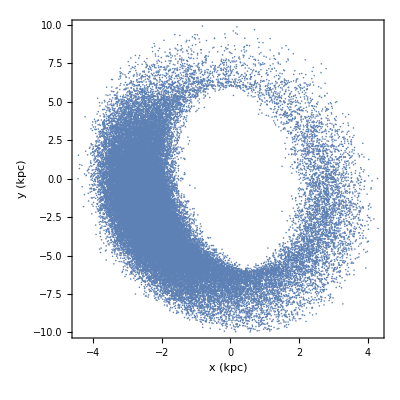

```mathematica
dmCords00xyr6to10RV=dmCordsLoose•RV⟦All,;;2⟧;
ListPlot[dmCords00xyr6to10RV, FrameLabel->{"x (kpc)","y (kpc)"}, Axes->True, Frame->True, FrameStyle->Directive[Thickness[0.003],FontSize->15,FontFamily->"Times"],FrameTicksStyle->Directive[Black, 15], LabelStyle->Directive[14], AspectRatio->1]
```

#### MW-Only